```mathematica
KneserGraph[n_,r_]:=KneserGraph[n,r]=Graph[TwoWayRule@@@Select[Subsets[Subsets[Range[n],{r}],{2}],DisjointQ@@#&]]
```

```mathematica
EKR[n_,r_,x_]:=Select[Subsets[Range[n],{r}],MemberQ[#,x]&]
```

```mathematica
HM[n_,r_,a_,x_]:=Prepend[Select[Subsets[Range[n],{r}],MemberQ[#,x]&&ContainsAny[#,a]&],a]
```

```mathematica
shift[i_,j_,F_]:=If[Length[#]==1,#[True],Join[#[True],Sort/@(#[False]/.j->i)]]&[GroupBy[F,MemberQ[#,i]||!MemberQ[#,j]||MemberQ[F,Sort[#/.j->i]]&]]
```

```mathematica
stabilize[F_,n_]:=Fold[shift[First[#2],Last[#2],#1]&,F,Table[{i,j},{i,1,n},{j,i+1,n}]]
```

```mathematica
SortBy[Subsets[Range[9],{4}],{Reverse}]
```

{{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,6},{1,2,4,6},{1,3,4,6},{2,3,4,6},{1,2,5,6},{1,3,5,6},{2,3,5,6},{1,4,5,6},{2,4,5,6},{3,4,5,6},{1,2,3,7},{1,2,4,7},{1,3,4,7},{2,3,4,7},{1,2,5,7},{1,3,5,7},{2,3,5,7},{1,4,5,7},{2,4,5,7},{3,4,5,7},{1,2,6,7},{1,3,6,7},{2,3,6,7},{1,4,6,7},{2,4,6,7},{3,4,6,7},{1,5,6,7},{2,5,6,7},{3,5,6,7},{4,5,6,7},{1,2,3,8},{1,2,4,8},{1,3,4,8},{2,3,4,8},{1,2,5,8},{1,3,5,8},{2,3,5,8},{1,4,5,8},{2,4,5,8},{3,4,5,8},{1,2,6,8},{1,3,6,8},{2,3,6,8},{1,4,6,8},{2,4,6,8},{3,4,6,8},{1,5,6,8},{2,5,6,8},{3,5,6,8},{4,5,6,8},{1,2,7,8},{1,3,7,8},{2,3,7,8},{1,4,7,8},{2,4,7,8},{3,4,7,8},{1,5,7,8},{2,5,7,8},{3,5,7,8},{4,5,7,8},{1,6,7,8},{2,6,7,8},{3,6,7,8},{4,6,7,8},{5,6,7,8},{1,2,3,9},{1,2,4,9},{1,3,4,9},{2,3,4,9},{1,2,5,9},{1,3,5,9},{2,3,5,9},{1,4,5,9},{2,4,5,9},{3,4,5,9},{1,2,6,9},{1,3,6,9},{2,3,6,9},{1,4,6,9},{2,4,6,9},{3,4,6,9},{1,5,6,9},{2,5,6,9},{3,5,6,9},{4,5,6,9},{1,2,7,9},{1,3,7,9},{2,3,7,9},{1,4,7,9},{2,4,7,9},{3,4,7,9},{1,5,7,9},{2,5,7,9},{3,5,7,9},{4,5,7,9},{1,6,7,9},{2,6,7,9},{3,6,7,9},{4,6,7,9},{5,6,7,9},{1,2,8,9},{1,3,8,9},{2,3,8,9},{1,4,8,9},{2,4,8,9},{3,4,8,9},{1,5,8,9},{2,5,8,9},{3,5,8,9},{4,5,8,9},{1,6,8,9},{2,6,8,9},{3,6,8,9},{4,6,8,9},{5,6,8,9},{1,7,8,9},{2,7,8,9},{3,7,8,9},{4,7,8,9},{5,7,8,9},{6,7,8,9}}

```mathematica
partitions[n_,k_]:=With[{lexi=SortBy[Subsets[Range[n],{k}],{Reverse}]},Select[Table[Subgraph[KneserGraph[n,k],lexi⟦;;i⟧],{i,Binomial[n-1,k-1],Binomial[n,k]}],!ConnectedGraphQ[#]&&(Binomial[n,k]-VertexCount[#])/(Length@ConnectedComponents[#])≤n/k-1&]]
```

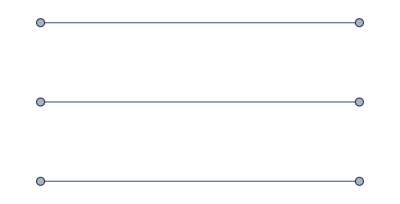

```mathematica
partitions[5,2]
```


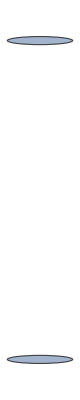
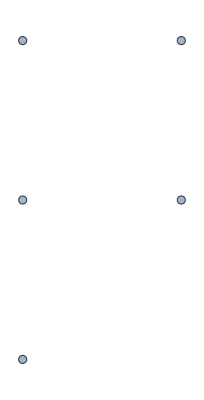
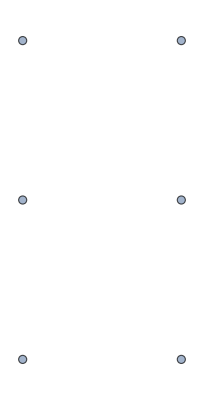
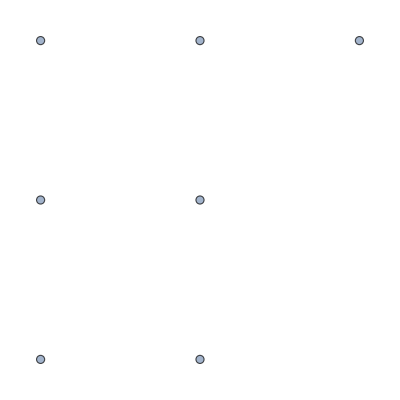
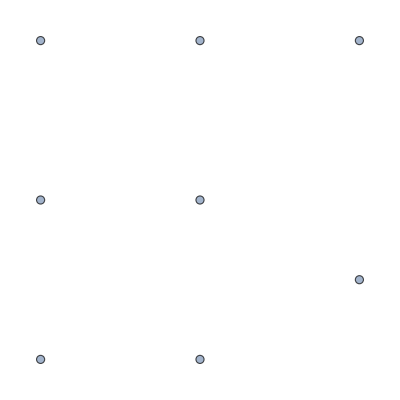
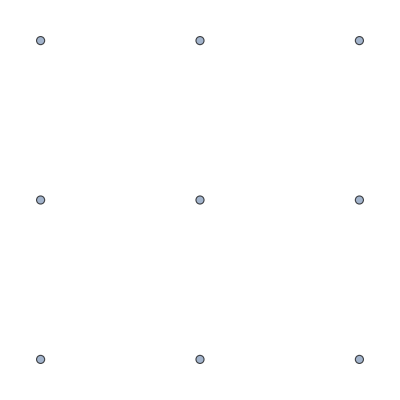
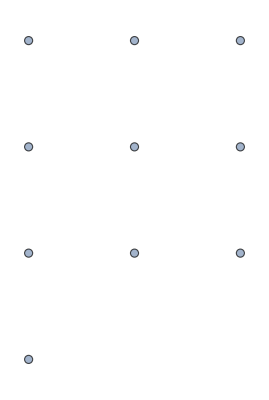
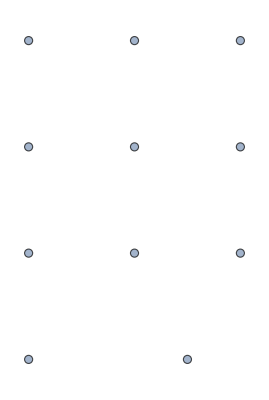
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{lexi=SortBy[Subsets[Range[9],{4}],{Reverse}],n=9,k=4},Table[Subgraph[KneserGraph[n,k],lexi⟦;;i⟧],{i,Binomial[n,k]}]]
```

```mathematica
With[{lexi=SortBy[Subsets[Range[11],{5}],{Reverse}],n=11,k=5},Table[Subgraph[KneserGraph[n,k],lexi⟦;;i⟧],{i,1,Binomial[n,k]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphDistance[KneserGraph[9,4],{1,2,3,4},#]&/@SortBy[Subsets[Range[9],{4}],{Reverse}]⟦Binomial[8,4];;⟧
```

{1,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,4,4,4,4,4,4,3,3,3,3,3,3,3,3,1,4,4,4,4,4,4,3,3,3,3,3,3,3,3,1,3,3,3,3,1,1}